## Double Pendulum

## Completed and Analyzed in class, February 25, 2025

This is the tenth notebook for you to complete.

### Double Pendulum — Angular Accelerations — Recap

Copied over from the theory we just presented (without derivation):

α_1=-1/16cos(θ_2-θ_1)+1/16 ω_2^2 sin(θ_2-θ_1)-4 π^2 sinθ_1

α_2=-4 α_1 cos(θ_2-θ_1)-4 ω_1^2 sin(θ_2-θ_1)-16 π^2 sinθ_2

Well, that is easy enough to code up:

```mathematica
alpha1[theta1_,theta2_,omega1_,omega2_]:=-1/16 Cos[theta2-theta1]+1/16 omega2^2 Sin[theta2-theta1]-4 Pi^2 Sin[theta1];

alpha2[theta1_,theta2_,omega1_,omega2_]:=-4alpha1[theta1,omega1,theta2,omega2]Cos[theta2-theta1]-4 omega1^2 Sin[theta2-theta1]-16 Pi^2 Sin[theta2];
```

### Initial Conditions

First set up the duration. Let’s also define steps and deltaT while we are at it:

```mathematica
tInitial = 0.0;
tFinal = 120.0;
steps = 7200;
deltaT = (tFinal - tInitial)/steps;
```

We’ll pull longer pendulum back to -45° and the shorter one we’ll just let hang straight down:

```mathematica
theta1Initial=-45°;
theta2Initial=0°;
omega1Initial=0.0;
omega2Initial=0.0;
```

```mathematica
initialConditions={tInitial,theta1Initial,theta2Initial,omega1Initial,omega2Initial}
```

{0.,-45 °,0,0.,0.}

### Second-Order Runge-Kutta — Double Pendulum — Recap

Also copied over from the theory:

t_(i+1)=t_i+Δt

θ_1^*=θ_1(t_i)+ω_1(t_i)·Δt/2

θ_2^*=θ_2(t_i)+ω_2(t_i)·Δt/2

ω_1^*=ω_1(t_i)+α_1(θ_1,ω_1,θ_2,ω_2)·Δt/2

ω_2^*=ω_2(t_i)+α_2(θ_1,ω_1,θ_2,ω_2)·Δt/2

ω_1(t_(i+1))=ω_1(t_i)+α_1(θ_1^*,ω_1^*,θ_2^*,ω_2^*)·Δt

ω_2(t_(i+1))=ω_2(t_i)+α_2(θ_1^*,ω_1^*,θ_2^*,ω_2^*)·Δt

θ_1(t_(i+1))=θ_1(t_i)+ (ω_1(t_i)+ω_1(t_(i+1)))Δt/2

θ_2(t_(i+1))=θ_2(t_i)+ (ω_2(t_i)+ω_2(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:=(
curTime=cc[[1]];
curTheta1=cc[[2]];
curTheta2=cc[[3]];
curOmega1=cc[[4]];
curOmega2=cc[[5]];
newTime=curTime+deltaT;
theta1Star=curTheta1+curOmega1 deltaT/2;
theta2Star=curTheta2+curOmega2 deltaT/2;
omega1Star=curOmega1+alpha1[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
omega2Star=curOmega2+alpha2[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
newOmega1=curOmega1+alpha1[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newOmega2=curOmega2+alpha2[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newTheta1=curTheta1+(curOmega1+newOmega1)deltaT/2;
newTheta2=curTheta2+(curOmega2+newOmega2)deltaT/2;
{newTime,newTheta1,newTheta2,newOmega1,newOmega2}
)
rungeKutta2[initialConditions]
```

{0.0166667,-0.781525,-0.0109835,0.464839,-1.31802}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=Transpose[NestList[rungeKutta2,initialConditions,steps]]
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
times=rk2Results[[1]];
theta1s=rk2Results[[2]];
theta2s=rk2Results[[3]];
```

```mathematica
times
```

```mathematica
timesAndTheta1s=Transpose[{times,theta1s}];
timesAndTheta2s=Transpose[{times,theta2s}];
```

ListLinePlot::prng: Value of option PlotRange -> {{0,120.},{-2.37400455637679×10^622,5.45285034728065×10^622}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

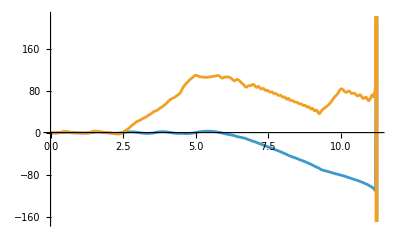

```mathematica
ListLinePlot[{timesAndTheta1s,timesAndTheta2s}]
```

#### A Graphic

The graphics work is straightforward but a little time-consuming, and not terribly instructive, so it is already all done:

```mathematica
coupledOscillatorGraphic[positionList_]:=Graphics[{
width=10;
buffer=0.5;
netWidth=width-2 buffer;
wallHeight=1.0;
numberOfSprings=n+1;
(* the next line makes a gray rectangle *)
{EdgeForm[Thin],Gray,Polygon[{{0,-1},{width,-1},{width,1},{0,1}}]},
(* the next two lines make the walls *)
Line[{{buffer,-wallHeight/2},{buffer,wallHeight/2}}],
Line[{{width-buffer,-wallHeight/2},{width-buffer,wallHeight/2}}],
(* finally we draw all the points *)
Table[Style[Point[{positionList[[j]]+netWidth/numberOfSprings j+buffer,0.0}],PointSize[0.03]],{j,n}]
}]
(* A little test to see if our code at least draws equally-spaced points when the positions are all zero: *)
coupledOscillatorGraphic[Table[0.0,n]]
```

Table::nliter: Non-list iterator n at position 2 does not evaluate to a real numeric value.

Table::iterb: Iterator {j,n} does not have appropriate bounds.

-Graphics-

#### Animating The Graphics